```mathematica
(* calculando b to s gamma contribucion de 2HDM III, aqui usamos 0309103 y 9802391 *)
(* input parameters *)
(* Vts Vtb Vcb *)
α=1/137.056 ;
mc =1.27 ;
mb=4.8;
mt=164;
mw=80.399 ;
mz=91.1876 ;
μ=mb ;
μw=mw ;
αsz=0.119 ;
(* funcion cinematica *)
z=0.31;
fz=1-8 z^2+8 z^6-z^8-24 z^4 Log[z] ;
(* strong coupling constant *)
v[y_]=1-23/3 αsz/(2 π)Log[mz/y];
αs[y_]=αsz/v[y](1-116/23 αsz/(4 π)Log[v[y]]/v[y]) ;
(* operators at mw scale *)
xtw=(mt/mw)^2 ;
yth=(mt/mH)^2 ;
(* mH=500 ; U2=1 ; U1=1 ; *)
c20=1 ;
c7sm[x_]=(3 x^3-2 x^2)/(4 (x-1)^4)Log[x]+(-8 x^3-5 x^2+7 x)/(24 (x-1)^3) ;
c8sm[x_]=(-3 x^2)/(4 (x-1)^4)Log[x]+(-x^3+5 x^2+2x)/(8 (x-1)^3) ;
c7yy[x_]=x ((-8 x^2-5 x+7)/(72(x-1)^3)+(3 x^2-2 x)/(12 (x-1)^4)Log[x]) ;
c7xy[x_]=x/12((-5 x^2+8 x-3+(6 x-4) Log[x])/(x-1)^3);
c8yy[x_]=(-x^3+5 x^2+2 x)/(24(x-1)^3)-(3 x^2)/(12 (x-1)^4)Log[x] ;
c8xy[x_]=x/4((- x^2+4 x-3-2  Log[x])/(x-1)^3);
c70[x_,y_]=c7sm[x]+U1^2 c7yy[y]+U2*U1 c7xy[y];
c80[x_,y_]=c8sm[x]+U1^2 c8yy[y]+U2*U1 c8xy[y] ; 
(* effective operator c7 *)
η=αs[mw]/αs[μ] ;
c7ef[x_,y_]=η^(16/23)c70[x,y]+8/3 (η^(14/23)-η^(16/23)) c80[x,y]+c20 (2.2996 η^(14/23)-1.0880 η^(16/23)-3/7 η^(6/23)-1/14 η^(-12/23)-0.6494 η^0.4086-0.0380 η^-0.4230-0.0185 η^-0.8994-0.0057 η^0.1456) ;
(* the branching is by def *)
(* ((Vts*Vtb)/Vcb)^2 is CKM factor included numerically and the semileptonic ratio from pdg *)
BrLO[mH_,U1_,U2_]=10.08/100 0.971 (6 α)/(π fz)(c7ef[xtw,yth])^2 ;
```

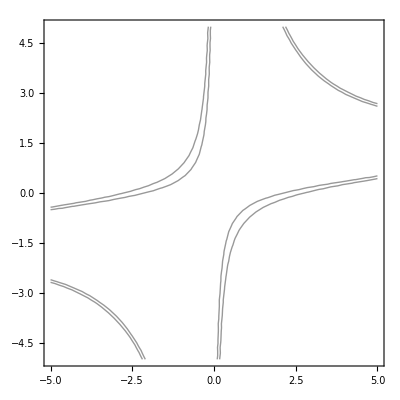

```mathematica
fig1=ContourPlot[BrLO[400,U1,-U2],{U1,-5,5},{U2,-5,5}, Contours->{ 3.27*10^-4,3.76*10^-4}, ContourShading->False]
```

```mathematica
(* NLO *)
λ1 =0.5 ;
λ2=-0.12 ;
kz=1-(2 αs[μ])/(3 π)((π^2-31/4)(1-z)^2+1.5)+1/mb^2(λ1/2+(3*λ2)/2 (1-4((1-z^2)^4)/fz)) ;
c1ef=η^(6/23)-η^(-12/23) ;
c2ef=2/3 η^(6/23)+1/3 η^(-12/23) ;
c8ef=η^(14/23)c80[xtw,yth]+0.8623 η^(14/23)-0.9135 η^0.4086+0.0873  η^-0.4230-0.0571 η^-0.8994+0.0209 η^0.1456 ;
fg=N[0.29^2] ;
r2=2/243 (-833+144 π^2 fg^1.5+(1728-180 π^2-1296 Zeta[3]+(1296-324 π^2)Log[fg]+108 Log[fg]^2+36 Log[fg]^3)  fg+(648+72 π^2+(432-216 π^2) Log[fg]+36 Log[fg]^3) fg^2+(-54-84 π^2+1092 Log[fg]-756 Log[fg]^2) fg^3)+(16 π ⅈ)/81(-5+(45-3 π^2+9 Log[fg]+9 Log[fg]^2) fg+(-3 π^2+9 Log[fg]^2)fg^2+(28-12 Log[fg]) fg^3) ;
r1=-1/6 r2 ;
r7= 32/9-8/9 π^2 ;
r8=-4/27 (-33+2 π^2-6 π ⅈ) ;
vmu[x_,y_]= αs[μ]/(4 π) (c1ef r1+ c2ef r2+c7ef[xtw,yth] r7+c8ef r8 -16/3 c7ef[xtw,yth]);
e0[x_]= (x(x^2+11 x-18))/(12 (x-1)^3)+(x^2 (4 x^2-16 x+15) Log[x])/(6 (x-1)^4)-2/3 Log[x]-2/3 ;
eh[x_]=x/36 ((7 x^3-36 x^2+45 x -16 +(18 x-12) Log[x])/(x-1)^4) ;
c41=  e0[xtw]+ 2/3 Log[μw^2/mw^2]+U1^ 2 eh[yth];
w7sm =(-16 x^4-122 x^3+80 x^2-8 x)/(9 (x-1)^4) PolyLog[2,1-1/x] +(6 x^4+46  x^3-28 x^2)/(3 (x-1)^5)Log[x]^2+(-102 x^5-588 x^4-2262 x^3+3244 x^2-1364 x +208)/(81 (x-1)^5) Log[x] +(1646  x^4+12205 x^3-10740 x^2+2509 x-436)/(486 (x-1)^4);
m7sm= 1/(81 (x-1)^5)(82 x^5+301 x^4+703 x^3-2197 x^2+1319 x-208-(162 x^4+1242 x^3-756 x^2) Log[x]) ;
t7sm= x/3 ((47 x^3-63 x^2+9 x+7-(18 x^3+30 x^2-24 x) Log[x])/(x-1)^5 ) ;
c71sm[x_]=w7sm+m7sm   Log[μw^2/mw^2] +t7sm (Log[mt^2/μw^2]-4/3) ;
w7yy=(2 x)/9 ((8 x^3-37 x^2+18 x)/(x-1)^4 PolyLog[2,1-1/x]+(3 x^3+23 x^2-14 x)/(x-1)^5 Log[x]^2+(21 x^4-192 x^3-174 x^2+251 x -50)/(9 (x-1)^5) Log[x]+(-1202 x^3+7569 x^2-5436 x+797)/(108  (x-1)^4) ) -4/9 eh[x] ;
m7yy=x/(27 (x-1)^5)(-14 x^4+149 x^3-153 x^2-13 x+31-(18 x^3+138 x^2-84 x) Log[x]) ;
c71yy[x_]=w7yy+m7yy   Log[μw^2/mH^2] +t7sm/3 (Log[mt^2/μw^2]-4/3) ;
w7xy=4/3((8 x^3-28 x^2+12 x)/(3 (x-1)^3)PolyLog[2,1-1/x]+(3 x^3+14 x^2-8 x)/(3 (x-1)^4)Log[x]^2+(4 x^4-24 x^3+2 x^2+6 x)/(3 (x-1)^4) Log[x]+(-2 x^3+13 x^2-7 x)/(x-1)^3 )  ;
m7xy= 2/(9 (x-1)^4)(-8 x^4+55 x^3-68 x^2+21 x-(6 x^3+28 x^2-16 x) Log[x]) ;
t7xy= (2 x)/3 ((13 x^2-20 x+7-(6 x^2+4 x-4) Log[x])/(x-1)^4 ) ;

c71xy[x_]=w7xy+m7xy   Log[μw^2/mH^2] +t7xy (Log[mt^2/μw^2]-4/3) ;  
c71  = c71sm[xtw]+U1^2 c71yy[yth]+U1*U2 c71xy[yth]  ;

w8sm= (-4 x^4+40 x^3+41 x^2+ x)/(6 (x-1)^4) PolyLog[2,1-1/x] +(-17 x^3-31 x^2)/(2 (x-1)^5)Log[x]^2+(-210 x^5+1086 x^4+4893 x^3+2857 x^2-1994 x +280)/(216 (x-1)^5) Log[x] +(737 x^4-14102 x^3-28209 x^2+610 x-508)/(1296 (x-1)^4) ;
m8sm=  1/(108 (x-1)^5)(77 x^5-475 x^4-1111 x^3+607 x^2+1042 x-140+(918 x^3+1674 x^2) Log[x]) ;
t8sm=2 x ((-x^3-9 x^2+9 x+1+(6 x^2+6 x) Log[x])/(x-1)^5 )   ;
w8yy= x/6 ((13 x^3-17 x^2+30 x)/(x-1)^4 PolyLog[2,1-1/x]-(17 x^2+31 x)/(x-1)^5 Log[x]^2+(42 x^4+318 x^3+1353 x^2+817 x -226)/(36 (x-1)^5) Log[x]+(-4451 x^3+7650 x^2-18153 x+1130)/(216  (x-1)^4) ) -1/6 eh[x]  ;
m8yy=  x/(36 (x-1)^5)(-7 x^4+25 x^3-279 x^2+223 x+38+(102 x^2+186 x) Log[x]) ;
w8xy= 1/3((17 x^3-25 x^2+36 x)/(2 (x-1)^3)PolyLog[2,1-1/x]-(17 x^2+19 x)/(x-1)^4 Log[x]^2+(14 x^4-12 x^3+187 x^2+3 x)/(4 (x-1)^4) Log[x]-(3 (29 x^3-44 x^2+143 x))/(8 (x-1)^3) ) ;
m8xy= 1/(6 (x-1)^4)(-7 x^4+23 x^3-97 x^2+81 x+(34 x^2+38 x) Log[x]) ;
t8xy=  2 x ((-x^2-4 x+5+(4 x+2) Log[x])/(x-1)^4 ) ;
c81sm[x_]= w8sm+m8sm   Log[μw^2/mw^2] +t8sm (Log[mt^2/μw^2]-4/3)  ;

c81yy[x_]= w8yy+m8yy   Log[μw^2/mH^2] +t8sm/3 (Log[mt^2/μw^2]-4/3) ;
c81xy[x_]= w8xy+m8xy   Log[μw^2/mH^2] +t8xy (Log[mt^2/μw^2]-4/3) ;
c81  = c81sm[xtw]+U1^2 c81yy[yth]+U1*U2 c81xy[yth]    ;
c11ef=15 +6 Log[μw^2/mw^2]  ;
c71eff=η^(39/23)c71+8/3 (η^(37/23)-η^(39/23)) c81+c80[xtw,yth]  (-7164416/357075 η^(14/23)+297664/14283 η^(16/23)+256868/14283 η^(37/23)-6698884/357075 η^(39/23)) +37208/4761(η^(39/23)-η^(16/23)) c70[xtw,yth]+(4661194/816831 η^(14/23)-8516/2217 η^(16/23)-1.9043 η^0.4086-0.1008 η^-0.4230+0.1216 η^-0.8994+0.0183 η^0.1456)η c41 -17.3023 η^(14/23)+8.5027 η^(16/23)+4.5508 η^(6/23)+0.7519 η^(-12/23) +2.0040 η^0.4086+0.7476 η^-0.4230-0.5385 η^-0.8994+0.0914 η^0.1456+(9.9372 η^(14/23)-7.4878 η^(16/23)+1.2688 η^(6/23)-0.2925 η^(-12/23) -2.2923 η^0.4086-0.1461 η^-0.4230+0.1239 η^-0.8994+0.0812 η^0.1456 ) η+(0.5784 η^(14/23)-0.3921 η^(16/23)-0.1429 η^(6/23)+0.0476 η^(-12/23) -0.1275 η^0.4086+0.0317 η^-0.4230+0.0078 η^-0.8994-0.0031 η^0.1456) η c11ef ;
c7eft=c7ef[xtw,yth]+αs[μ]/(4 π)c71eff ;
bd=c7eft+vmu[xtw,yth];
Gt[t_]=If[t<4, -2 ArcTan[√(t/(4-t))]^2,-π^2/2+2 Log[(√t+√(t-4))/2]^2-2 π ⅈ Log[(√t+√(t-4))/2]]; 

f220=(16 fg)/27 ∫_0^3.999 (1-fg t)^2 Abs[Gt[t]/t+0.5]^2 ⅆt ;
f22p=(16 fg)/27 ∫_4^11.89 (1-fg t)^2 Abs[Gt[t]/t+0.5]^2 ⅆt ;
f22=f220+f22p ;
f270=-(8 fg^2)/9∫_0^3.999 (1-fg t)(Gt[t]+0.5 t)ⅆt ;
f27p=-(8 fg^2)/9∫_4^11.89 (1-fg t)(Gt[t]+0.5 t)ⅆt ;
f27=f270+f27p ;

f11=f22/36 ;
f12=-f22/3;
f17=-f27/6 ;
f18=-f28/6 ;
f28=-f27/3 ;
f78=8/9 (25/12-π^2/6) ;
f88= 1/27(16/3-(4 π^2)/3) ;
A=αs[μ]/π  (c1ef^2 f11 +c1ef c2ef f12+c1ef c7ef[xtw,yth] f17 +c1ef c8ef f18 +c2ef^2 f22 +c2ef c7ef[xtw,yth] f27+c2ef c8ef f28+c7ef[xtw,yth] c8ef f78+c8ef^2 f88);
Δ= 1/mb^2 (λ1*0.5-4.5*λ2)c7ef[xtw,yth]^2+(-λ2/(9 mc^2))(c7ef[xtw,yth] (c2ef-c1ef/6));
```

```mathematica
brNLO[mH_,U1_,U2_]=N[Re[10.08/100*0.971 (6 α)/(π fz kz)(Abs[bd]^2+ A + Δ)]];
```

```mathematica
N[brNLO[150,0,0]]
```

0.000326466

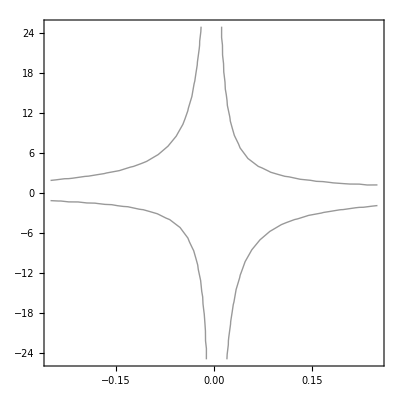

```mathematica
fig2=ContourPlot[brNLO[150,U1,-U2],{U1,-0.25,.25},{U2,-25,25}, Contours->{ 2.78*10^-4,4.26*10^-4}, ContourShading->False, PlotPoints->10]
```

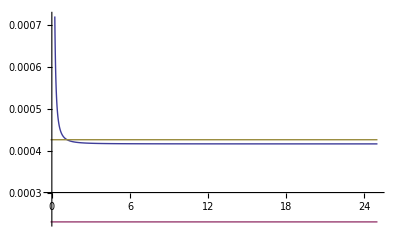

```mathematica
Plot[{brNLO[350,-1/U2,-U2],2.3*10^-4,4.26*10^-4},{U2,-0.1,25}]
```

```mathematica
brNLO[150,-0.1,-.1]
```

0.000328677

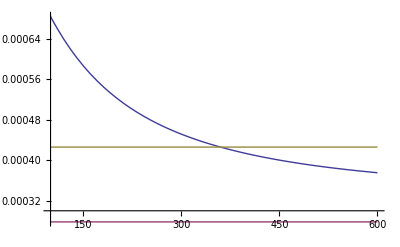

```mathematica
Plot[{brNLO[mH,-1,-1],2.78*10^-4,4.26*10^-4},{mH,100,600}]
```

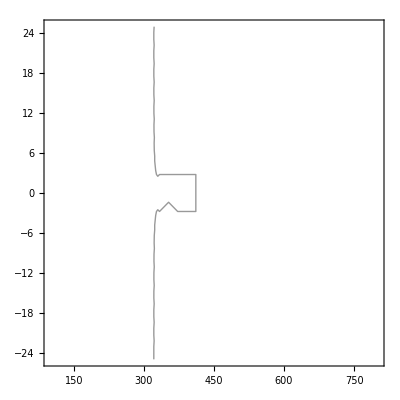

```mathematica
fig3=ContourPlot[brNLO[mH,-1/U2,-U2],{mH,100,800},{U2,-25,25}, Contours->{ 2.78*10^-4,4.26*10^-4}, ContourShading->False, PlotPoints->10]
```

```mathematica
(* Razon de H+->tau nu con H￿+-> tb en modelos 2 y 3 *)
bm=2.83; 
tm= 173.1;
tau=1.77;
RR[mH_,U1_,U2_]=(tau^2 U2^2 (1-tau^2/mH^2)^2)/(3 (1-tm^2/mH^2)^2(bm^2 U2^2+tm^2 U1^2-U2 U1(4 tm^2 bm^2)/(mH^2 (1-tm^2/mH^2)))) ;
RR2[mH_,U1_,U2_]=(tau^2 U1^2 (1-tau^2/mH^2)^2)/(3 (1-tm^2/mH^2)^2(bm^2 U2^2+tm^2 U1^2-U2 U1(4 tm^2 bm^2)/(mH^2 (1-tm^2/mH^2)))) ;
```

```mathematica
sp=OpenWrite["brs2800.dat", FormatType-> OutputForm]
lista={};
zetadR={};
type2={};
Do[If[brNLO[800,U1,-U2]≤4.26*10^-4&& brNLO[800,U1,-U2]≥ 2.78*10^-4  ,
Write[sp, N[U2], "  ",N[RR2[800,U1,U2]]];
(*caso a*)
(*calcule R*)
zetadR=AppendTo[zetadR,{U2,RR2[800,U1,U2]}];
type2=AppendTo[type2,{U2,RR[800,-1/U2,-U2]}];
AppendTo[lista,{U1,U2}];
];
,{U1,-0.5,0.5,0.01},{U2,-25,25,0.1}]
Close[sp]
```

OutputStream[brs2800.dat,45]

brs2800.dat

```mathematica
sp=OpenWrite["r2type2150.dat", FormatType-> OutputForm]
lista={};
type23={};
Do[If[brNLO[800,-1/U2,-U2]≤4.26*10^-4&& brNLO[800,-1/U2,-U2]≥ 2.78*10^-4  ,
Write[sp, N[U2], "  ",N[RR[800,U1,U2]]];

type23=AppendTo[type23,{U2,RR[800,-1/U2,-U2]}];
AppendTo[lista,{U1,U2}];
];
,{U1,-0.25,0.25,0.01},{U2,-.25,.25,0.01}]
Close[sp]
```

OutputStream[r2type2150.dat,48]

r2type2150.dat

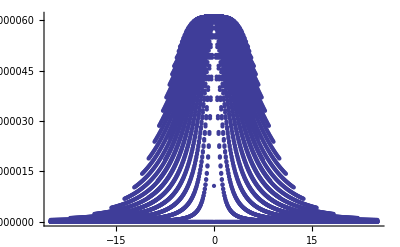

```mathematica
Fig6=ListPlot[zetadR]
```

```mathematica
Fig7=ListPlot[type23]
```

ListPlot::lpn: {{}} is not a list of numbers or pairs of numbers.

ListPlot[{}]

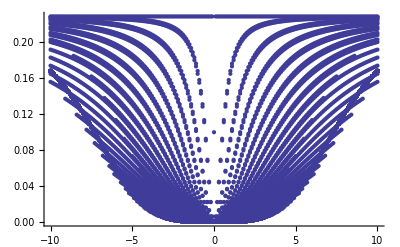

```mathematica
Show[Fig6,Fig7]
```

```mathematica
Export["R2800.dat",zetadR]
```

R2800.dat

```mathematica
Export["type2800.dat", type23]
```

type2800.dat